```mathematica
f[n_,s_]:=n^(1-s) s HarmonicNumber[n,1-s]-n^s (1-s) HarmonicNumber[n,s]-s+1/2
f2[n_,s_]:=(n^(1-s) s HarmonicNumber[n,1-s]+n^s (1-s) HarmonicNumber[n,s])-2n-1/2
f3[n_,s_]:=(n^s (1-s) HarmonicNumber[n,s]-n+s/2 -1/2)/n^(Re[s])
f3y[n_,s_]:=(1-s) HarmonicNumber[n,s]+(-n+s/2 -1/2)/n^s
f3x[n_,s_]:=n^s (1-s) HarmonicNumber[n,s]
```

```mathematica
N[f3y[31000000000,s]]-(1-s)Zeta[s]/.s->-.5+12I
```

-54.5543-53.3869 ⅈ

```mathematica
(1-s)Zeta[s]/.s->.5+1I
```

-0.650132-0.504986 ⅈ

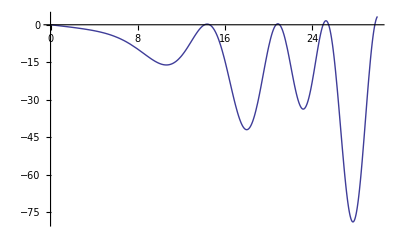

0.5+14.1347 ⅈ

```mathematica
Plot[Im@(f3y[1000000,.5+x I]),{x,0,30}]
```

```mathematica
FullSimplify[D[f3[n,s],s]]
```

(1-2 n^s (HarmonicNumber[n,s] (1+(-1+s) Log[n])+(-1+s) HarmonicNumber^(0,1)[n,s]))/(2 √n)

```mathematica
FullSimplify[D[Abs[n^s(1-s) j^-s],s]]
```

ⅇ^(-Re[s Log[j]]) (-n^s (1+(-1+s) Log[n]) Abs'[-n^s (-1+s)]-Abs[n^s (-1+s)] Log[j] Re'[s Log[j]])

```mathematica
Plot[Im@((1-(.5+x I))Zeta[.5+x I]),{x,0,30}]
```

-Graphics-

```mathematica
FullSimplify[(n^s (1-s) HarmonicNumber[n,s]-n+s/2 -1/2)/n^(Re[s])/.s->5+x I]
```

1/2 n^(-5+Im[x]) (4-2 n+ⅈ x-2 ⅈ n^(5+ⅈ x) (-4 ⅈ+x) HarmonicNumber[n,5+ⅈ x])

```mathematica
Expand[(n^s (1-s) HarmonicNumber[n,s]-n+s/2 -1/2)/n^s]
```

-n^(1-s)-n^-s/2+(n^-s s)/2+HarmonicNumber[n,s]-s HarmonicNumber[n,s]